```mathematica
(*\[Omega ] everything is by default in B frame unless stated otherwise*)
AωC[t] = {u1[t],u2[t],u3[t]};
AωB[t] = {u1[t],u2[t],u2[t]Tan[q2[t]]};
AαC[t] = Simplify[D[AωC[t],t] + Cross[AωB[t],AωC[t]]];
CDtoA[t] ={{Cos[q1[t]],-Sin[q1[t]],0},{Sin[q1[t]],Cos[q1[t]],0},{0,0,1}};
CAtoD[t]=Transpose[CDtoA[t] ]; 
CBtoD[t] ={{1,0,0},{0,Sin[q2[t]],-Cos[q2[t]]},{0,Cos[q2[t]],Sin[q2[t]]}};
CDtoB[t] = Transpose[CBtoD[t]];
rOPInertial[t] = {q4[t],q5[t],0};
AvPInertial[t] = {u4[t],u5[t],0};
AvP[t] = CDtoB[t].CAtoD[t].AvPInertial[t];
(*apply two point formula, both fixed in B*)
rPCstar={0,R,0};
AvCstar[t] = Simplify[AvP[t]+ Cross[AωB[t],rPCstar]]
```

{-R Tan[q2[t]] u2[t]+Cos[q1[t]] u4[t]+Sin[q1[t]] u5[t],Sin[q2[t]] (-Sin[q1[t]] u4[t]+Cos[q1[t]] u5[t]),R u1[t]+Cos[q2[t]] (Sin[q1[t]] u4[t]-Cos[q1[t]] u5[t])}

```mathematica
(*/.{q1'[t]->u2[t]/Cos[q2[t]],q2'[t]->-u1[t],q3'[t]->u3[t]-u2[t]Tan[q2[t]],q4'[t]->u4[t],q5'[t]->u5[t]}*)
AαB[t]=D[AωB[t],t]/.q2'[t]->-u1[t]
AaP[t] = CDtoB[t].CAtoD[t].D[AvPInertial[t],t]
AaCstar[t] = Simplify[AaP[t] + Cross[AωB[t],Cross[AωB[t],rPCstar]]+Cross[AαB[t],rPCstar]]
```

{u1'[t],u2'[t],-Sec[q2[t]]^2 u1[t] u2[t]+Tan[q2[t]] u2'[t]}

{Cos[q1[t]] u4'[t]+Sin[q1[t]] u5'[t],-Sin[q1[t]] Sin[q2[t]] u4'[t]+Cos[q1[t]] Sin[q2[t]] u5'[t],Cos[q2[t]] Sin[q1[t]] u4'[t]-Cos[q1[t]] Cos[q2[t]] u5'[t]}

{R (1+Sec[q2[t]]^2) u1[t] u2[t]-R Tan[q2[t]] u2'[t]+Cos[q1[t]] u4'[t]+Sin[q1[t]] u5'[t],-R u1[t]^2-R Tan[q2[t]]^2 u2[t]^2+Sin[q2[t]] (-Sin[q1[t]] u4'[t]+Cos[q1[t]] u5'[t]),R Tan[q2[t]] u2[t]^2+R u1'[t]+Cos[q2[t]] (Sin[q1[t]] u4'[t]-Cos[q1[t]] u5'[t])}

```mathematica
(*two point formula both fixed in C*)
AvChatInertial[t]= Simplify[CDtoA[t].CBtoD[t].(AvCstar[t]+Cross[AωC[t],-rPCstar[t]])];
(*alternatively*)
BωC[t] = AωC[t]-AωB[t];
CvChat[t] = Cross[rPCstar,BωC[t]];
AvChatInertial[t] = Simplify[AvPInertial[t]+ CDtoA[t].CBtoD[t]. CvChat[t]]
```

{-R Tan[q2[t]] u2[t]+R u3[t],0,0}

{R Cos[q1[t]] (-Tan[q2[t]] u2[t]+u3[t])+u4[t],R Sin[q1[t]] (-Tan[q2[t]] u2[t]+u3[t])+u5[t],0}

{-R Cos[q1[t]] Tan[q2[t]] u2[t]+R Cos[q1[t]] u3[t]+u4[t],-R Sin[q1[t]] Tan[q2[t]] u2[t]+R Sin[q1[t]] u3[t]+u5[t],0}

```mathematica
(* partial velocities: choose AvCstar and AwC to be motion variables *)
v1[t] = Coefficient[AvCstar[t],u1[t]];
v2[t] = Coefficient[AvCstar[t],u2[t]];
v3[t] = Coefficient[AvCstar[t],u3[t]];
v4[t] = Coefficient[AvCstar[t],u4[t]];
v5[t] = Coefficient[AvCstar[t],u5[t]];
ω1[t] = Coefficient[AωC[t],u1[t]];
ω2[t] = Coefficient[AωC[t],u2[t]];
ω3[t] = Coefficient[AωC[t],u3[t]];
ω4[t] = Coefficient[AωC[t],u4[t]];
ω5[t] = Coefficient[AωC[t],u5[t]];
```

```mathematica
(*active force*)
RInertial[t] = {0,0,-m g};
R[t] = CDtoB[t].CAtoD[t].RInertial[t];
(*active torque applied at Cstar*)
T[t] = Cross[rPCstar, R[t]];
F1[t] =Simplify[(v1[t].R[t]+ ω1[t].T[t])];
F2[t] =Simplify[(v2[t].R[t]+ ω2[t].T[t])];
F3[t] =Simplify[(v3[t].R[t]+ ω3[t].T[t])];
F4[t] =Simplify[(v4[t].R[t]+ ω4[t].T[t])];
F5[t] =Simplify[(v5[t].R[t]+ ω5[t].T[t])];
(*inertial force*)
Rstar[t] = - m AaCstar[t];
(*inertial torque: B frame, can use B instead of C cuz disk is symmetric*)
ICstar={{1/4m R^2,0,0},{0,1/4 m R^2,0},{0,0,1/2 m R^2}}
Tstar[t] = -ICstar.AαC[t] - Cross[AωC[t],ICstar.AωC[t]]
```

{{(m R^2)/4,0,0},{0,(m R^2)/4,0},{0,0,(m R^2)/2}}

{-1/4 m R^2 u2[t] u3[t]-1/4 m R^2 (-Tan[q2[t]] u2[t]^2+u2[t] u3[t]+u1'[t]),1/4 m R^2 u1[t] u3[t]-1/4 m R^2 (u1[t] (Tan[q2[t]] u2[t]-u3[t])+u2'[t]),-1/2 m R^2 u3'[t]}

```mathematica
F1star[t] =(v1[t].Rstar[t]+ ω1[t].Tstar[t]);
F2star[t] =(v2[t].Rstar[t]+ ω2[t].Tstar[t]);
F3star[t] =(v3[t].Rstar[t]+ ω3[t].Tstar[t]);
F4star[t] =(v4[t].Rstar[t]+ ω4[t].Tstar[t]);
F5star[t] =(v5[t].Rstar[t]+ ω5[t].Tstar[t]);
```

```mathematica
Eqn1[t]=Simplify[F1[t]+F1star[t]]
Eqn2[t]=Simplify[F2[t]+F2star[t]]
Eqn3[t]=Simplify[F3[t]+F3star[t]]
Eqn4[t]=Simplify[F4[t]+F4star[t]]
Eqn5[t]=Simplify[F5[t]+F5star[t]]
```

-1/4 m R (8 g Sin[q2[t]]+3 R Tan[q2[t]] u2[t]^2+2 R u2[t] u3[t]+5 R u1'[t]+4 Cos[q2[t]] Sin[q1[t]] u4'[t]-4 Cos[q1[t]] Cos[q2[t]] u5'[t])

1/4 m R (R u1[t] ((3+4 Sec[q2[t]]^2) Tan[q2[t]] u2[t]+2 u3[t])-(R+4 R Tan[q2[t]]^2) u2'[t]+4 Tan[q2[t]] (Cos[q1[t]] u4'[t]+Sin[q1[t]] u5'[t]))

-1/2 m R^2 u3'[t]

-1/4 m Cos[q2[t]] (4 R Sin[q1[t]] Tan[q2[t]] u1[t]^2+2 R Cos[q1[t]] (3+Cos[2 q2[t]]) Sec[q2[t]]^3 u1[t] u2[t]+4 (R Sec[q2[t]]^2 Sin[q1[t]] Tan[q2[t]] u2[t]^2+R Sin[q1[t]] u1'[t]+Sec[q2[t]] (-R Cos[q1[t]] Tan[q2[t]] u2'[t]+u4'[t])))

m R Cos[q1[t]] Sin[q2[t]] u1[t]^2-1/2 m R (3+Cos[2 q2[t]]) Sec[q2[t]]^2 Sin[q1[t]] u1[t] u2[t]+m (R Cos[q1[t]] Sec[q2[t]] Tan[q2[t]] u2[t]^2+R Cos[q1[t]] Cos[q2[t]] u1'[t]+R Sin[q1[t]] Tan[q2[t]] u2'[t]-u5'[t])

```mathematica
m=1;
R=1;
g=9.81;
tf = 0.5;
solK = NDSolve[{q1'[t]==u2[t]/Cos[q2[t]],q2'[t]==-u1[t],q3'[t]==u3[t]-u2[t]Tan[q2[t]],q4'[t]==u4[t],q5'[t]==u5[t],Eqn1[t]==0,Eqn2[t]==0,Eqn3[t]==0,Eqn4[t]==0,Eqn5[t]==0,q1[0]==0,q2[0]==0.1,q3[0]==0,q4[0]==0,q5[0]==0,u1[0]==0,u2[0]==0,u3[0]==0,u4[0]==0,u5[0]==0},{q1[t],q2[t],q3[t],q4[t],q5[t],u1[t],u2[t],u3[t],u4[t],u5[t]},{t,0,tf},Method->{"EquationSimplification"->"Residual"}]
```

{{q1[t]→InterpolatingFunction[…][t],q2[t]→InterpolatingFunction[…][t],q3[t]→InterpolatingFunction[…][t],q4[t]→InterpolatingFunction[…][t],q5[t]→InterpolatingFunction[…][t],u1[t]→InterpolatingFunction[…][t],u2[t]→InterpolatingFunction[…][t],u3[t]→InterpolatingFunction[…][t],u4[t]→InterpolatingFunction[…][t],u5[t]→InterpolatingFunction[…][t]}}

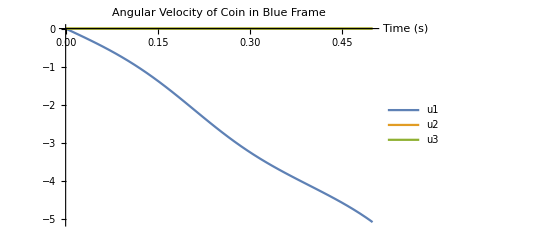

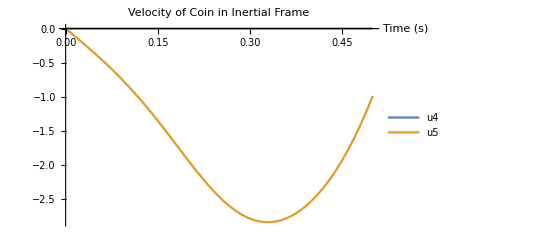

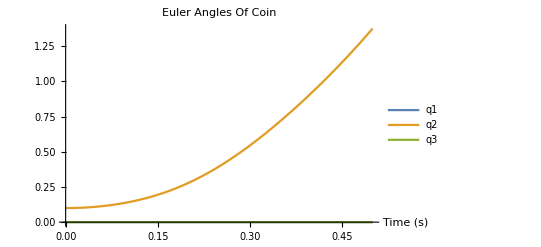

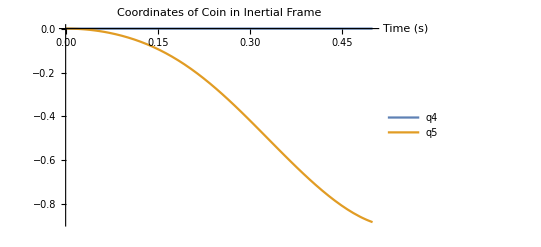

```mathematica
Plot[Evaluate[{u1[t],u2[t],u3[t]}/. solK],{t,0,tf},PlotRange->All,
PlotLegends->{"u1","u2","u3"},AxesLabel->{"Time (s)"},PlotLabel->"Angular Velocity of Coin in Blue Frame"]
Plot[Evaluate[{u4[t],u5[t]}/. solK],{t,0,tf},PlotRange->All,
PlotLegends->{"u4","u5","u6"},AxesLabel->{"Time (s)"},PlotLabel->"Velocity of Coin in Inertial Frame"]
Plot[Evaluate[{q1[t],q2[t],q3[t]}/. solK],{t,0,tf},PlotRange->All,
PlotLegends->{"q1","q2","q3"},AxesLabel->{"Time (s)"},PlotLabel->"Euler Angles Of Coin"]
Plot[Evaluate[{q4[t],q5[t]}/. solK],{t,0,tf},PlotRange->All,
PlotLegends->{"q4","q5","q6"},AxesLabel->{"Time (s)"},PlotLabel->"Coordinates of Coin in Inertial Frame"]
```

9.81 Cos[q2[t]]+1/2 (u1[t]^2/4+u2[t]^2/4+u3[t]^2/2)+1/2 (Sin[q2[t]]^2 (-Sin[q1[t]] u4[t]+Cos[q1[t]] u5[t])^2+(-Tan[q2[t]] u2[t]+Cos[q1[t]] u4[t]+Sin[q1[t]] u5[t])^2+(u1[t]+Cos[q2[t]] (Sin[q1[t]] u4[t]-Cos[q1[t]] u5[t]))^2)^2

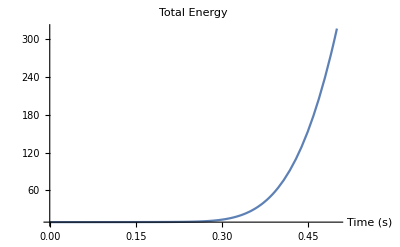

```mathematica
Energy[t] = 1/2 m (AvCstar[t].AvCstar[t])^2 + 1/2 Transpose[AωC[t]].ICstar.AωC[t]+ m g R Cos[q2[t]]
Plot[Evaluate[Energy[t]/. solK],{t,0,tf},PlotRange->All,AxesLabel->{"Time (s)"},PlotLabel->"Total Energy"]
```

```mathematica
(*Lagrange*)
```

```mathematica
L[t] = Simplify[1/2 m (AvCstar[t].AvCstar[t])^2 +1/2 Transpose[AωC[t]].ICstar.AωC[t]- m g R Cos[q2[t]]/.{u1[t]->-q2'[t],u2[t]->q1'[t]Cos[q2[t]],u3[t]->q3'[t]+q1'[t]Sin[q2[t]],u4[t]->q4'[t],u5[t]->q5'[t]}]
```

1/8 m (-8 g R Cos[q2[t]]+R^2 Cos[q2[t]]^2 q1'[t]^2+R^2 q2'[t]^2+2 R^2 (Sin[q2[t]] q1'[t]+q3'[t])^2+4 (Sin[q2[t]]^2 (Sin[q1[t]] q4'[t]-Cos[q1[t]] q5'[t])^2+(-R Sin[q2[t]] q1'[t]+Cos[q1[t]] q4'[t]+Sin[q1[t]] q5'[t])^2+(R q2'[t]+Cos[q2[t]] (-Sin[q1[t]] q4'[t]+Cos[q1[t]] q5'[t]))^2)^2)

```mathematica
L1[t] = Simplify[D[L[t],q1[t]] -  D[D[L[t],q1'[t]],t]]
L2[t]=Simplify[D[L[t],q2[t]] -  D[D[L[t],q2'[t]],t]]
L3[t]=Simplify[D[L[t],q3[t]] -  D[D[L[t],q3'[t]],t]]
L4[t]=Simplify[D[L[t],q4[t]] -  D[D[L[t],q4'[t]],t]]
L5[t]=Simplify[D[L[t],q5[t]] -  D[D[L[t],q5'[t]],t]]
```

1/4 m R (R Sin[2 q2[t]] q1'[t] q2'[t]-2 R Cos[q2[t]] q2'[t] (Sin[q2[t]] q1'[t]+q3'[t])+8 Cos[q2[t]] q2'[t] (-R Sin[q2[t]] q1'[t]+Cos[q1[t]] q4'[t]+Sin[q1[t]] q5'[t]) (Sin[q2[t]]^2 (Sin[q1[t]] q4'[t]-Cos[q1[t]] q5'[t])^2+(-R Sin[q2[t]] q1'[t]+Cos[q1[t]] q4'[t]+Sin[q1[t]] q5'[t])^2+(R q2'[t]+Cos[q2[t]] (-Sin[q1[t]] q4'[t]+Cos[q1[t]] q5'[t]))^2)+8 (Sin[q2[t]] q1'[t] (Sin[q1[t]] q4'[t]-Cos[q1[t]] q5'[t])-Cos[q2[t]] q2'[t] (Cos[q1[t]] q4'[t]+Sin[q1[t]] q5'[t])) (Sin[q2[t]]^2 (Sin[q1[t]] q4'[t]-Cos[q1[t]] q5'[t])^2+(-R Sin[q2[t]] q1'[t]+Cos[q1[t]] q4'[t]+Sin[q1[t]] q5'[t])^2+(R q2'[t]+Cos[q2[t]] (-Sin[q1[t]] q4'[t]+Cos[q1[t]] q5'[t]))^2)-R Cos[q2[t]]^2 q1''[t]-2 R Sin[q2[t]] (Cos[q2[t]] q1'[t] q2'[t]+Sin[q2[t]] q1''[t]+q3''[t])+8 Sin[q2[t]] (Sin[q2[t]]^2 (Sin[q1[t]] q4'[t]-Cos[q1[t]] q5'[t])^2+(-R Sin[q2[t]] q1'[t]+Cos[q1[t]] q4'[t]+Sin[q1[t]] q5'[t])^2+(R q2'[t]+Cos[q2[t]] (-Sin[q1[t]] q4'[t]+Cos[q1[t]] q5'[t]))^2) (-q1'[t] (R Cos[q2[t]] q2'[t]+Sin[q1[t]] q4'[t]-Cos[q1[t]] q5'[t])-R Sin[q2[t]] q1''[t]+Cos[q1[t]] q4''[t]+Sin[q1[t]] q5''[t])+16 Sin[q2[t]] (-R Sin[q2[t]] q1'[t]+Cos[q1[t]] q4'[t]+Sin[q1[t]] q5'[t]) (Cos[q2[t]] Sin[q2[t]] q2'[t] (Sin[q1[t]] q4'[t]-Cos[q1[t]] q5'[t])^2+Sin[q2[t]]^2 (Sin[q1[t]] q4'[t]-Cos[q1[t]] q5'[t]) (q1'[t] (Cos[q1[t]] q4'[t]+Sin[q1[t]] q5'[t])+Sin[q1[t]] q4''[t]-Cos[q1[t]] q5''[t])+(-R Sin[q2[t]] q1'[t]+Cos[q1[t]] q4'[t]+Sin[q1[t]] q5'[t]) (-q1'[t] (R Cos[q2[t]] q2'[t]+Sin[q1[t]] q4'[t]-Cos[q1[t]] q5'[t])-R Sin[q2[t]] q1''[t]+Cos[q1[t]] q4''[t]+Sin[q1[t]] q5''[t])+(R q2'[t]+Cos[q2[t]] (-Sin[q1[t]] q4'[t]+Cos[q1[t]] q5'[t])) (Sin[q2[t]] q2'[t] (Sin[q1[t]] q4'[t]-Cos[q1[t]] q5'[t])+R q2''[t]-Cos[q2[t]] (q1'[t] (Cos[q1[t]] q4'[t]+Sin[q1[t]] q5'[t])+Sin[q1[t]] q4''[t]-Cos[q1[t]] q5''[t]))))

1/8 m R (8 g Sin[q2[t]]-R Sin[2 q2[t]] q1'[t]^2+4 R Cos[q2[t]] q1'[t] (Sin[q2[t]] q1'[t]+q3'[t])+16 (R Cos[q2[t]] Sin[q2[t]] q1'[t]^2+Sin[q2[t]] q2'[t] (Sin[q1[t]] q4'[t]-Cos[q1[t]] q5'[t])-Cos[q2[t]] q1'[t] (Cos[q1[t]] q4'[t]+Sin[q1[t]] q5'[t])) (Sin[q2[t]]^2 (Sin[q1[t]] q4'[t]-Cos[q1[t]] q5'[t])^2+(-R Sin[q2[t]] q1'[t]+Cos[q1[t]] q4'[t]+Sin[q1[t]] q5'[t])^2+(R q2'[t]+Cos[q2[t]] (-Sin[q1[t]] q4'[t]+Cos[q1[t]] q5'[t]))^2)-2 R q2''[t]-16 (Sin[q2[t]]^2 (Sin[q1[t]] q4'[t]-Cos[q1[t]] q5'[t])^2+(-R Sin[q2[t]] q1'[t]+Cos[q1[t]] q4'[t]+Sin[q1[t]] q5'[t])^2+(R q2'[t]+Cos[q2[t]] (-Sin[q1[t]] q4'[t]+Cos[q1[t]] q5'[t]))^2) (Sin[q2[t]] q2'[t] (Sin[q1[t]] q4'[t]-Cos[q1[t]] q5'[t])+R q2''[t]-Cos[q2[t]] (q1'[t] (Cos[q1[t]] q4'[t]+Sin[q1[t]] q5'[t])+Sin[q1[t]] q4''[t]-Cos[q1[t]] q5''[t]))-32 (R q2'[t]+Cos[q2[t]] (-Sin[q1[t]] q4'[t]+Cos[q1[t]] q5'[t])) (Cos[q2[t]] Sin[q2[t]] q2'[t] (Sin[q1[t]] q4'[t]-Cos[q1[t]] q5'[t])^2+Sin[q2[t]]^2 (Sin[q1[t]] q4'[t]-Cos[q1[t]] q5'[t]) (q1'[t] (Cos[q1[t]] q4'[t]+Sin[q1[t]] q5'[t])+Sin[q1[t]] q4''[t]-Cos[q1[t]] q5''[t])+(-R Sin[q2[t]] q1'[t]+Cos[q1[t]] q4'[t]+Sin[q1[t]] q5'[t]) (-q1'[t] (R Cos[q2[t]] q2'[t]+Sin[q1[t]] q4'[t]-Cos[q1[t]] q5'[t])-R Sin[q2[t]] q1''[t]+Cos[q1[t]] q4''[t]+Sin[q1[t]] q5''[t])+(R q2'[t]+Cos[q2[t]] (-Sin[q1[t]] q4'[t]+Cos[q1[t]] q5'[t])) (Sin[q2[t]] q2'[t] (Sin[q1[t]] q4'[t]-Cos[q1[t]] q5'[t])+R q2''[t]-Cos[q2[t]] (q1'[t] (Cos[q1[t]] q4'[t]+Sin[q1[t]] q5'[t])+Sin[q1[t]] q4''[t]-Cos[q1[t]] q5''[t]))))

-1/2 m R^2 (Cos[q2[t]] q1'[t] q2'[t]+Sin[q2[t]] q1''[t]+q3''[t])

m (-2 R^2 Sin[q2[t]]^2 q1'[t]^2+4 R Sin[q2[t]] q1'[t] (Cos[q1[t]] q4'[t]+Sin[q1[t]] q5'[t])-2 (R^2 q2'[t]^2+q4'[t]^2+q5'[t]^2-2 R Cos[q2[t]] q2'[t] (Sin[q1[t]] q4'[t]-Cos[q1[t]] q5'[t]))) (R Sin[q1[t]] Sin[q2[t]] q1'[t]^2-2 R Cos[q1[t]] Cos[q2[t]] q1'[t] q2'[t]+R Sin[q1[t]] Sin[q2[t]] q2'[t]^2-R Cos[q1[t]] Sin[q2[t]] q1''[t]-R Cos[q2[t]] Sin[q1[t]] q2''[t]+q4''[t])+4 m (R Cos[q1[t]] Sin[q2[t]] q1'[t]+R Cos[q2[t]] Sin[q1[t]] q2'[t]-q4'[t]) (Cos[q2[t]] Sin[q2[t]] q2'[t] (Sin[q1[t]] q4'[t]-Cos[q1[t]] q5'[t])^2+Sin[q2[t]]^2 (Sin[q1[t]] q4'[t]-Cos[q1[t]] q5'[t]) (q1'[t] (Cos[q1[t]] q4'[t]+Sin[q1[t]] q5'[t])+Sin[q1[t]] q4''[t]-Cos[q1[t]] q5''[t])+(-R Sin[q2[t]] q1'[t]+Cos[q1[t]] q4'[t]+Sin[q1[t]] q5'[t]) (-q1'[t] (R Cos[q2[t]] q2'[t]+Sin[q1[t]] q4'[t]-Cos[q1[t]] q5'[t])-R Sin[q2[t]] q1''[t]+Cos[q1[t]] q4''[t]+Sin[q1[t]] q5''[t])+(R q2'[t]+Cos[q2[t]] (-Sin[q1[t]] q4'[t]+Cos[q1[t]] q5'[t])) (Sin[q2[t]] q2'[t] (Sin[q1[t]] q4'[t]-Cos[q1[t]] q5'[t])+R q2''[t]-Cos[q2[t]] (q1'[t] (Cos[q1[t]] q4'[t]+Sin[q1[t]] q5'[t])+Sin[q1[t]] q4''[t]-Cos[q1[t]] q5''[t])))

-m (-2 R^2 Sin[q2[t]]^2 q1'[t]^2+4 R Sin[q2[t]] q1'[t] (Cos[q1[t]] q4'[t]+Sin[q1[t]] q5'[t])-2 (R^2 q2'[t]^2+q4'[t]^2+q5'[t]^2-2 R Cos[q2[t]] q2'[t] (Sin[q1[t]] q4'[t]-Cos[q1[t]] q5'[t]))) (R Cos[q1[t]] Sin[q2[t]] q1'[t]^2+2 R Cos[q2[t]] Sin[q1[t]] q1'[t] q2'[t]+R Cos[q1[t]] Sin[q2[t]] q2'[t]^2+R Sin[q1[t]] Sin[q2[t]] q1''[t]-R Cos[q1[t]] Cos[q2[t]] q2''[t]-q5''[t])-4 m (-R Sin[q1[t]] Sin[q2[t]] q1'[t]+R Cos[q1[t]] Cos[q2[t]] q2'[t]+q5'[t]) (Cos[q2[t]] Sin[q2[t]] q2'[t] (Sin[q1[t]] q4'[t]-Cos[q1[t]] q5'[t])^2+Sin[q2[t]]^2 (Sin[q1[t]] q4'[t]-Cos[q1[t]] q5'[t]) (q1'[t] (Cos[q1[t]] q4'[t]+Sin[q1[t]] q5'[t])+Sin[q1[t]] q4''[t]-Cos[q1[t]] q5''[t])+(-R Sin[q2[t]] q1'[t]+Cos[q1[t]] q4'[t]+Sin[q1[t]] q5'[t]) (-q1'[t] (R Cos[q2[t]] q2'[t]+Sin[q1[t]] q4'[t]-Cos[q1[t]] q5'[t])-R Sin[q2[t]] q1''[t]+Cos[q1[t]] q4''[t]+Sin[q1[t]] q5''[t])+(R q2'[t]+Cos[q2[t]] (-Sin[q1[t]] q4'[t]+Cos[q1[t]] q5'[t])) (Sin[q2[t]] q2'[t] (Sin[q1[t]] q4'[t]-Cos[q1[t]] q5'[t])+R q2''[t]-Cos[q2[t]] (q1'[t] (Cos[q1[t]] q4'[t]+Sin[q1[t]] q5'[t])+Sin[q1[t]] q4''[t]-Cos[q1[t]] q5''[t])))

```mathematica
tf=1;
solL = NDSolve[{L1[t]==0,L2[t]==0,L3[t]==0,L4[t]==0,L5[t]==0,q1[0]==0,q2[0]==0.01,q3[0]==0,q4[0]==0,q5[0]==0,q1'[0]==0,q2'[0]==1,q3'[0]==0,q4'[0]==0,q5'[0]==0},{q1[t],q2[t],q3[t],q4[t],q5[t]},{t,0,tf},Method->{"EquationSimplification"->"Residual"}]
```

{{q1[t]→InterpolatingFunction[…][t],q2[t]→InterpolatingFunction[…][t],q3[t]→InterpolatingFunction[…][t],q4[t]→InterpolatingFunction[…][t],q5[t]→InterpolatingFunction[…][t]}}

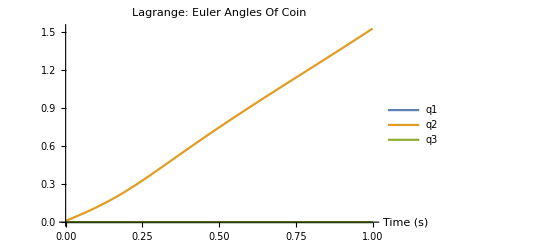

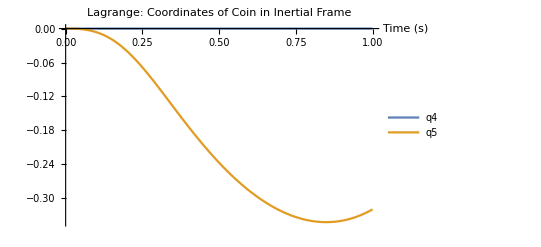

```mathematica
Plot[Evaluate[{q1[t],q2[t],q3[t]}/. solL],{t,0,tf},PlotRange->All,
PlotLegends->{"q1","q2","q3"},AxesLabel->{"Time (s)"},PlotLabel->"Lagrange: Euler Angles Of Coin"]
Plot[Evaluate[{q4[t],q5[t]}/. solL],{t,0,tf},PlotRange->All,
PlotLegends->{"q4","q5","q6"},AxesLabel->{"Time (s)"},PlotLabel->"Lagrange: Coordinates of Coin in Inertial Frame"]
```

```mathematica
EnergyL[t] = 1/2 m (AvCstar[t].AvCstar[t])^2 + 1/2 Transpose[AωC[t]].ICstar.AωC[t]+ m g R Cos[q2[t]]/.{u1[t]->-q2'[t],u2[t]->q1'[t]Cos[q2[t]],u3[t]->q3'[t]+q1'[t]Sin[q2[t]],u4[t]->q4'[t],u5[t]->q5'[t]}
Plot[Evaluate[EnergyL[t]/. solL],{t,0,tf},PlotRange->All,AxesLabel->{"Time (s)"},PlotLabel->"Lagrange: Total Energy"]
```

9.81 Cos[q2[t]]+1/2 (1/4 Cos[q2[t]]^2 q1'[t]^2+1/4 q2'[t]^2+1/2 (Sin[q2[t]] q1'[t]+q3'[t])^2)+1/2 (Sin[q2[t]]^2 (-Sin[q1[t]] q4'[t]+Cos[q1[t]] q5'[t])^2+(-Sin[q2[t]] q1'[t]+Cos[q1[t]] q4'[t]+Sin[q1[t]] q5'[t])^2+(-q2'[t]+Cos[q2[t]] (Sin[q1[t]] q4'[t]-Cos[q1[t]] q5'[t]))^2)^2

{9.81 Cos[InterpolatingFunction[…][t]]+1/2 (1/4 Cos[InterpolatingFunction[…][t]]^2 q1'[t]^2+1/4 q2'[t]^2+1/2 (Sin[InterpolatingFunction[…][t]] q1'[t]+q3'[t])^2)+1/2 (Sin[InterpolatingFunction[…][t]]^2 (-Sin[InterpolatingFunction[…][t]] q4'[t]+Cos[InterpolatingFunction[…][t]] q5'[t])^2+(-Sin[InterpolatingFunction[…][t]] q1'[t]+Cos[InterpolatingFunction[…][t]] q4'[t]+Sin[InterpolatingFunction[…][t]] q5'[t])^2+(-q2'[t]+Cos[InterpolatingFunction[…][t]] (Sin[InterpolatingFunction[…][t]] q4'[t]-Cos[InterpolatingFunction[…][t]] q5'[t]))^2)^2}

-Graphics-